# Реализация программы постобработки при генерации случайных бит с помощью алгоритма Бабкина

## Инициализация функций

```mathematica
η1 = 0.4
η2 = 0.5
c = 1
μ = 10
```

0.4

0.5

1

10

```mathematica
P[x_,y_] := Exp[-1/2(η1 + η2)μ] 1/(x!y!)((η1 μ)/2)^x((η2 μ)/2)^y
```

```mathematica
Bessel[ν_,z_]:= (1/2 z)^ν Sum[((1/4 z^2)^k)/(k!Gamma[ν+k+1]),{k,0,∞}]
```

```mathematica
Poison[x_] := (η1/η2)^(x/2)Bessel[Abs[x],μ(η1 η2)^(1/2) ]Exp[-1/2(η1 + η2)μ]
Gauss[x_]:=1/(√(Pi (η1 μ+η1 μ)))Exp[-(x - ((η1 μ)/2-(η1 μ)/2))^2/(η1 μ+η1 μ)]
```

Сместим координаты так, чтобы распределение было 
почти симметричным относительно полуосей:

```mathematica
Integrate[Gauss[x],{x,-∞,∞}]
```

1.

```mathematica
xarr =Sum[z Poison[z],{z,-6μ,6μ}]
```

-0.5

```mathematica
xmax = First[FindMaximum[Poison[z],{z,-6μ,6μ}]]
```

0.194081

```mathematica
PoisonSym[x_]:= Poison[x+xarr]
```

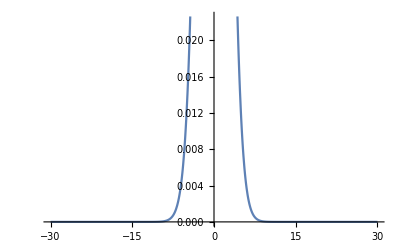

```mathematica
Plot[PoisonSym[x],{x,-3μ,3μ}]
```

## Подготовка измерительной шкалы

```mathematica
f[x_, y_] :=Sum[PoisonSym[z],{z,x,y}]
```

Возьмем диапазон порядка удвоенного среднего числа фотонов в системе

```mathematica
l =μ
```

10

```mathematica
f[-l,l]
```

0.999969

Перенормируем центрированную функцию

```mathematica
NewPoisonSym [x_, Const_]:= Const PoisonSym[x]
```

```mathematica
Const =x/. Last[NSolve[Sum[NewPoisonSym[z,x] ,{z,-l,l}]==  1, x]]
```

1.00003

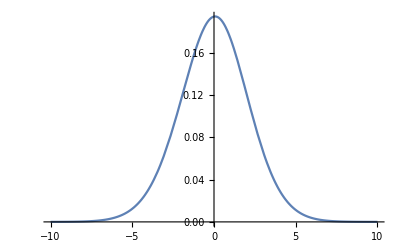

```mathematica
Plot[NewPoisonSym[x,Const],{x,-l,l}]
```

Получим указанное количество разбиений для обрезанной шкалы

```mathematica
Table[{Ceiling[y],Floor[y+l/2^(Log2[5]-1) ]},{y,-l,l-l/2^(Log2[5]-1) + 0.00000000001*5,l/2^(Log2[5]-1)+0.00000000001}]
```

{{-10,-6},{-5,-2},{-1,2},{3,6},{7,10}}

Посчитаем вероятности попасть в каждый отрезок, 
учитывая, что число фотонов - величина дискретная

```mathematica
fnew[x_, y_] :=Sum[NewPoisonSym[z, Const],{z,x,y}]
```

```mathematica
Tab1[M_] := Table[fnew[Ceiling[y],Floor[Floor[y+l/2^(M-1)] ]],
{y,-l,l-l/2^(M-1)+0.00000000001*2^M,l/2^(M-1)+0.00000000001}]
```

```mathematica
Tab1[2]
```

{0.0186149,0.574696,0.401707,0.00498124}

```mathematica
Sum[x,{x,Tab1[1]}]
```

1.

## Реализация функций для подсчета среднего количества бит, которое можно извлечь

Таблица с необходимым количеством переменных, по которым нужно 
суммировать (их на 1 меньше, чем отрезков на шкале) и диапазоном для их суммирования

```mathematica
Numbers[M_] :=Table[Subscript[n, i],{i,1,2^M-1}]
Perem[N1_,Num_]:= Table[{Num[[j]],0,N1-Sum[Num[[z]],
{z,1,j-1}]},{j,1,Dimensions[Num][[1]]}]
```

```mathematica
Perem[10,Numbers[2]]
```

{{n_1,0,10},{n_2,0,10-n_1},{n_3,0,10-n_1-n_2}}

Функция, которая дает оценку среднего количества 
извлеченных из системы бит в расчете на одно измерение

n - число измерений;
М - степень разбиения (всего 2^М отрезков на шкале);
T - таблица с вероятностями;
Num - таблица для суммирования (предыдущий блок)

```mathematica
Bits[n_,M_,T_,Num_]:= N[Sum[(n!)/((n-Sum[i,{i,Num}])!∏_(i=1)^(2^M-1) (Num[[i]]!))
Floor[Log2[(n!)/((n-Sum[i,{i,Num}])!∏_(i=1)^(2^M-1) Num[[i]]!)]]
T[[2^M]]^(n-Sum[i,{i,Num}])∏_(i=1)^(2^M-1) T[[i]]^Num[[i]], Evaluate[Sequence @@ Perem[n,Num]]]]
```

```mathematica
Bits[10,2,Tab1[2], Numbers[2]]
```

6.9338

Энтропия Шеннона для сравнения

```mathematica
H[T_] := N[-Sum[T[[i]]Log2[T[[i]]],{i,1,First[Dimensions[T]]}]]
```

```mathematica
10*H[Tab1[2]]
```

11.3291

## Реализация алгоритма

Зададим число измерений, степень разбиения и таблицу биномиальных коэффициентов

```mathematica
n1 = 10
Coeffs = Table[Table[Binomial[i-1,j] ,{i,1,n1}],{j,1,n1-1}]
```

10

{{0,1,2,3,4,5,6,7,8,9},{0,0,1,3,6,10,15,21,28,36},{0,0,0,1,4,10,20,35,56,84},{0,0,0,0,1,5,15,35,70,126},{0,0,0,0,0,1,6,21,56,126},{0,0,0,0,0,0,1,7,28,84},{0,0,0,0,0,0,0,1,8,36},{0,0,0,0,0,0,0,0,1,9},{0,0,0,0,0,0,0,0,0,1}}

```mathematica
m = 2
Tab1[m]
```

2

{0.0186149,0.574696,0.401707,0.00498124}

Имитируем результаты измерения

```mathematica
Outs = RandomInteger[{1,2^m},n1]
```

{2,4,2,1,3,1,1,4,3,2}

Таблица с позициями номеров выпадающих отрезков. Начинаем с 1-го, 
затем последующие записываем “зачеркивая” предыдущие.
В конце останутся отрезки одного класса, “рабочих” классов на 1 меньше

```mathematica
Positions = Table[Select[Range[Length[Select[Outs,MemberQ[Range[i,2^m],# ]&]]],Select[Outs,MemberQ[Range[i,2^m],# ]&][[#]]==i&],{i,1,2^m-1}]
```

{{4,6,7},{1,3,7},{2,4}}

```mathematica
Positions  = Select[Positions,#≠ {}&]
```

{{4,6,7},{1,3,7},{2,4}}

Посчитаем количество возможных элементов на каждой итерации

```mathematica
NumNums = Prepend[Table[Length[Positions[[i]]],{i,1,Length[Positions]}],0]
```

{0,3,3,2}

```mathematica
PowerClasses = Table[Binomial[n1 -Sum[NumNums[[j-1]],{j,2,i}],NumNums[[i]]] ,{i,2,Length[NumNums] }]
```

{120,35,6}

Посчитаем номера наших последовательностей на каждой итерации

```mathematica
Num[Pos_] :=Sum[Coeffs[[i]][[Pos[[i]]]],{i,1,Length[Pos]}]
```

```mathematica
Nums = Table[Num[Positions[[i]]],{i,1,Length[Positions]}]
```

{33,21,4}

Переведем в двоичное представление (мощности классов и номера выпавших последовательностей)
Затем для удобства исключим вычеркнем слагаемое 2^0 из номеров

```mathematica
Powers2 =Table[Reverse[IntegerDigits[PowerClasses[[i]],2]],{i,1,Length[PowerClasses]}]
```

{{0,0,0,1,1,1,1},{1,1,0,0,0,1},{0,1,1}}

```mathematica
Powers2to2 =Table[Select[Range[Length[Powers2[[i]]]],Powers2[[i]][[#]] ==1&] - 1,{i,1,Length[Powers2]}]
```

{{3,4,5,6},{0,1,5},{1,2}}

```mathematica
Drafts = Table[IntegerDigits[Nums[[i]],2],{i,1,Length[Nums]}]
```

{{1,0,0,0,0,1},{1,0,1,0,1},{1,0,0}}

Таблица с диапазонами классов на каждой итерации (начало, конец, нужно бит для нумерации)

```mathematica
PowerClass[iter_] := Prepend[Table[{Sum[2^(Powers2to2[[iter]][[j]]),{j,1,i}],Sum[2^(Powers2to2[[iter]][[j]]),{j,1,i+1}]-1,Powers2to2[[iter]][[i+1]]},{i,1,Length[Powers2to2[[iter]]]-1}],{0,2^(Powers2to2[[iter]][[1]])-1,Powers2to2[[iter]][[1]]}]
PowerClass[3]
```

{{0,1,1},{2,5,2}}

Выпишем, сколько нужно бит для нумерации элементов в классе, в который мы попали (для всех итераций)

```mathematica
NumBits = Table[First[Select[Table[If[PowerClass[j][[i]][[1]]<=Nums[[j]] <=PowerClass[j][[i]][[2]],PowerClass[j][[i]][[3]],-1],{i,1,Length[PowerClass[j]]}],# ≠-1&]],{j,1,Length[Nums]}]
```

{5,5,2}

Обрежем или добавим нули слева в двоичном представлении номеров последовательностей 
на каждой итерации, после чего произведем конкатенацию

```mathematica
X =Table[Flatten[If[Length[Drafts[[i]]]≤ NumBits[[i]], Prepend[Drafts[[i]],Table[0,{j,1,Abs[Length[Drafts[[i]]]- NumBits[[i]]]}]], Drop[Drafts[[i]],Length[Drafts[[i]]] - NumBits[[i]]]]],{i,1,Length[NumBits]}]
```

{{0,0,0,0,1},{1,0,1,0,1},{0,0}}

```mathematica
Flatten[X]
```

{0,0,0,0,1,1,0,1,0,1,0,0}